# Pset02: molecular dynamics

## Part B: Triatomic reaction dynamics with Lennard-Jones potentials B1: The Lennard Jones Potential a)

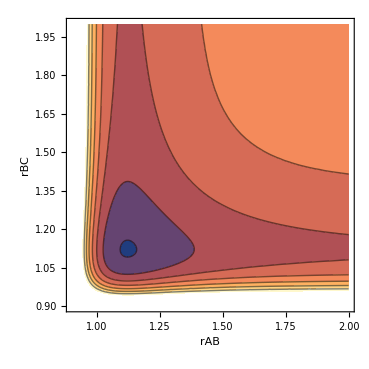

```mathematica
ClearAll["Global`*"]
Clear[Vlj, ϵ, rAB, rBC, σ, r];
ϵ=1.0;
σ=1.0;
Vlj[r_] = 4*ϵ*((σ/r)^12 - (σ/r)^6);
ContourPlot[Vlj[rAB] + Vlj[rBC] + Vlj[rAB+rBC], {rAB, 0.9, 2.0}, {rBC, 0.9, 2.0}, FrameLabel -> {"rAB","rBC"}]
```

```mathematica
solutions=Minimize[Vlj[rAB] + Vlj[rBC] + Vlj[rAB + rBC],{rAB,rBC}];
```

The configuration of the three atoms that gives a minimum potential energy of -2.03112 is the following:
	rAB = 1.12103 , rBC = 1.12103

## b)

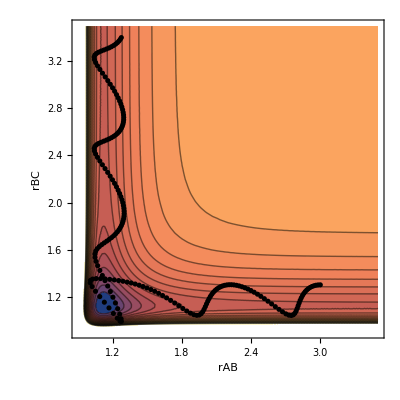

```mathematica
LJVerlet[ϵ_, σ_, time_, dt_, xA0_, xB0_, xC0_, vA0_, vB0_, vC0_] := Module[{},
	Subs={mA->1,mB->1,mC->1};
	nSteps=Round[time/dt];
	Flj[r_] = 24 ϵ(2(σ^12/r^13)-(σ^6/r^7));
	Vlj[r_] = 4*ϵ*((σ/r)^12 - (σ/r)^6);
	xA[0]=xA0;
	xB[0]=xB0;
	xC[0]=xC0;
	vA[0]=vA0;
	vB[0]=vB0;
	vC[0]=vC0;
	fA[0]=-Flj[xB[0]-xA[0]]-Flj[xC[0]-xA[0]];
	fB[0]=Flj[xB[0]-xA[0]]-Flj[xC[0]-xB[0]];
	fC[0]=Flj[xC[0]-xA[0]]+Flj[xC[0]-xB[0]];
	For[n=0,n<=nSteps,n++,
	xA[n+1]=xA[n]+vA[n]dt+dt^2 fA[n]/(2mA) /.Subs;
	xB[n+1]=xB[n]+vB[n]dt+dt^2 fB[n]/(2mB) /.Subs;
	xC[n+1]=xC[n]+vC[n]dt+dt^2 fC[n]/(2mC) /.Subs;
	fA[n+1]=-Flj[xB[n+1]-xA[n+1]]-Flj[xC[n+1]-xA[n+1]];
	fB[n+1]=Flj[xB[n+1]-xA[n+1]]-Flj[xC[n+1]-xB[n+1]];
	fC[n+1]=Flj[xC[n+1]-xA[n+1]]+Flj[xC[n+1]-xB[n+1]];
	vA[n+1]=vA[n]+(1/2)(fA[n]+fA[n+1])(dt/mA)/.Subs;
	vB[n+1]=vB[n]+(1/2)(fB[n]+fB[n+1])(dt/mB)/.Subs;
	vC[n+1]=vC[n]+(1/2)(fC[n]+fC[n+1])(dt/mC)/.Subs;
	];
	VPlot=ContourPlot[Vlj[rAB]+Vlj[rBC]+Vlj[rAB+rBC]/.Subs,{rAB,0.9,3.5},{rBC,0.9,3.5},Contours->20, FrameLabel -> {"rAB","rBC"}];
	trajData=Table[{xB[n]-xA[n],xC[n]-xB[n]},{n,0,nSteps}];
	trajPlot=ListPlot[trajData,PlotStyle->Black];
	Show[VPlot,trajPlot]
]
LJVerlet[ϵ=1.0, σ=1.0, time=4, dt=0.02, -3.0, 0.0, 1.3, 1.0, 0.0, 0.0]
```

The initial conditions here correspond to a incident atom colliding with a pair of bonded atoms.
Atom A (incident atom) ends up replacing Atom C to create a new AB bond.

## c)

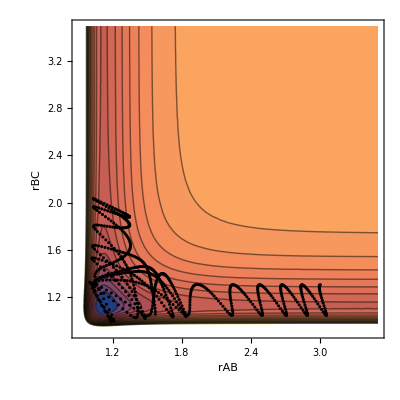

```mathematica
LJVerlet[ϵ=1.0, σ=1.0, time=15.0, dt=0.02, -3.0, 0.0, 1.3, 0.2, 0.0, 0.0]
```

Reducing the velocity of atom A from 1.0 to 0.2 results in the formation of a 3 atom complex. To understand why this forms,  we must look at how the relationship between kinetic and potential energy in the system. A bond between 2 atoms is preserved by potential energy. To break this bond, the kinetic energy of the atoms needs to overcome this potential energy. In our model, atom A failed to provide enough kinetic energy for atom B to overcome the potential barrier of its bond to atom C, resulting in a short-lived stretch in rBC bond and the formation of bond rAB.

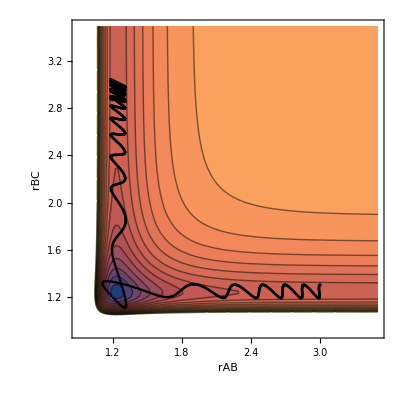

```mathematica
LJVerlet[ϵ=1.0, σ=1.1, time=15.0, dt=0.01, -3.0, 0.0, 1.3, 0.2, 0.0, 0.0]
```

Altering the sigma/epsilon values of the potential results in a change in the phase of the B-C vibration without altering its vibrational energy.

## d)

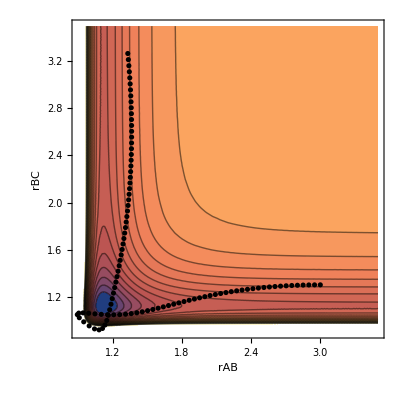

```mathematica
LJVerlet[ϵ=1.0, σ=1.0, time=1.0, dt=0.01, -3.0, 0.0, 1.3, 5.0, 0.0, 0.0]
```

## Part C: Triatomic reaction dynamics with LEPS potential C1: Dynamics on the LEPS potential a)